```mathematica
(* pie chart in Fig 1D *)
(* Sevahn Vorperian, Quake Lab *)
```

```mathematica
(* copying everything over here that is working because other notebook is a mess *)
```

```mathematica
fractions = Import["/Users/kayaneh/Documents/deconvolution/revision1/08012021_perComp_noEye_sigmat_18/adnci_v18_rmseAll_11282021/GEMs(Indiana)_sigMat18_avgCoefs_plasma_1129021.csv"];
```

```mathematica
roundPower = 0.1;
percentThresh = 1; (* percentage cutoff for stacked bar chart vs main pie *)
scalePercents = 100; (* scale all percentages by 100 *)
superSmallThresh = 0.1; (* percentage cutoff for cell types with small fractional contirbutions *)
sampleCenter = "GEMS/Indiana";
```

```mathematica
fractions
```

{{,GEMs (Indiana)},{erythrocyte/erythroid progenitor,0.275254},{platelet,0.162405},{monocyte,0.10399},{nk cell,0.0588493},{b cell,0.056898},{neutrophil,0.0418408},{endothelial cell,0.0371319},{mature conventional dendritic cell,0.0277872},{basophil,0.02387},{adventitial cell,0.0234096},{thymocyte,0.0217615},{intestinal tuft cell,0.0205127},{cell of skeletal muscle,0.0157827},{salivary gland cell,0.0125146},{myeloid progenitor,0.0121382},{salivary/bronchial secretory cell,0.0107099},{basal cell,0.00940845},{respiratory ciliated cell,0.00782098},{schwann cell,0.00726026},{pancreatic stellate cell,0.00698936},{intrahepatic cholangiocyte,0.00692464},{ionocyte/luminal epithelial cell of mammary gland,0.00659723},{medullary thymic epithelial cell,0.00644808},{kidney epithelial cell,0.00591275},{intestinal enterocyte,0.00547628},{t cell,0.00448861},{intestinal secretory cell,0.00406125},{pericyte cell,0.0035452},{basal cell of prostate epithelium,0.0024058},{prostate epithelia,0.00231534},{secretory cell,0.00220831},{respiratory secretory cell,0.00208285},{pancreatic alpha/beta cell,0.00193773},{type ii pneumocyte,0.00168046},{innate lymphoid cell,0.00154242},{hematopoietic stem cell,0.00148651},{plasmablast,0.00117442},{pancreatic ductal cell,0.000807176},{goblet cell,0.000628449},{tendon cell,0.000573702},{pancreatic acinar cell,0.000474921},{club cell/type i pneumocyte,0.00030753},{cardiac muscle cell,0.000234095},{macrophage,0.000173427},{pancreatic pp cell,0.000157524},{plasma cell,0.0000208529}}

```mathematica
fractions = fractions[[2;;]]; (* eliminate the center name *)
```

```mathematica
(* cellTypes = fractions[[1]][[2;;]] *)
cellTypes = fractions[[;;,1]]
```

{erythrocyte/erythroid progenitor,platelet,monocyte,nk cell,b cell,neutrophil,endothelial cell,mature conventional dendritic cell,basophil,adventitial cell,thymocyte,intestinal tuft cell,cell of skeletal muscle,salivary gland cell,myeloid progenitor,salivary/bronchial secretory cell,basal cell,respiratory ciliated cell,schwann cell,pancreatic stellate cell,intrahepatic cholangiocyte,ionocyte/luminal epithelial cell of mammary gland,medullary thymic epithelial cell,kidney epithelial cell,intestinal enterocyte,t cell,intestinal secretory cell,pericyte cell,basal cell of prostate epithelium,prostate epithelia,secretory cell,respiratory secretory cell,pancreatic alpha/beta cell,type ii pneumocyte,innate lymphoid cell,hematopoietic stem cell,plasmablast,pancreatic ductal cell,goblet cell,tendon cell,pancreatic acinar cell,club cell/type i pneumocyte,cardiac muscle cell,macrophage,pancreatic pp cell,plasma cell}

```mathematica
(* fractions =fractions[[2;;,2;;]][[1]] *)
fractions = fractions[[;;,2]]
```

{0.275254,0.162405,0.10399,0.0588493,0.056898,0.0418408,0.0371319,0.0277872,0.02387,0.0234096,0.0217615,0.0205127,0.0157827,0.0125146,0.0121382,0.0107099,0.00940845,0.00782098,0.00726026,0.00698936,0.00692464,0.00659723,0.00644808,0.00591275,0.00547628,0.00448861,0.00406125,0.0035452,0.0024058,0.00231534,0.00220831,0.00208285,0.00193773,0.00168046,0.00154242,0.00148651,0.00117442,0.000807176,0.000628449,0.000573702,0.000474921,0.00030753,0.000234095,0.000173427,0.000157524,0.0000208529}

```mathematica
Length[fractions]
```

46

```mathematica
Length[cellTypes]
```

46

```mathematica
(* fractions = Import["~/Documents/deconvolution/cellTypeFractions_10XDecon_07222020.xlsx"][[1]]; *)
```

```mathematica
contribs = fractions  (* excluded sample name and r, p-value, RMSE *)
```

{0.275254,0.162405,0.10399,0.0588493,0.056898,0.0418408,0.0371319,0.0277872,0.02387,0.0234096,0.0217615,0.0205127,0.0157827,0.0125146,0.0121382,0.0107099,0.00940845,0.00782098,0.00726026,0.00698936,0.00692464,0.00659723,0.00644808,0.00591275,0.00547628,0.00448861,0.00406125,0.0035452,0.0024058,0.00231534,0.00220831,0.00208285,0.00193773,0.00168046,0.00154242,0.00148651,0.00117442,0.000807176,0.000628449,0.000573702,0.000474921,0.00030753,0.000234095,0.000173427,0.000157524,0.0000208529}

```mathematica
Length[fractions]
```

46

```mathematica
Length[cellTypes]
```

46

```mathematica
(* first get the zero index *)
```

```mathematica
zeroIndex = Position[contribs, val_/;val ≤ 0]
```

{}

```mathematica
(* drop it from the contributions and drop the corresponding labels *)
```

```mathematica
nonZeroVals = Delete[contribs, zeroIndex];
```

```mathematica
nonZeroVals = nonZeroVals * scalePercents
```

{27.5254,16.2405,10.399,5.88493,5.6898,4.18408,3.71319,2.77872,2.387,2.34096,2.17615,2.05127,1.57827,1.25146,1.21382,1.07099,0.940845,0.782098,0.726026,0.698936,0.692464,0.659723,0.644808,0.591275,0.547628,0.448861,0.406125,0.35452,0.24058,0.231534,0.220831,0.208285,0.193773,0.168046,0.154242,0.148651,0.117442,0.0807176,0.0628449,0.0573702,0.0474921,0.030753,0.0234095,0.0173427,0.0157524,0.00208529}

```mathematica
Total[nonZeroVals]
```

100.

```mathematica
nonZeroCells = Delete[cellTypes, zeroIndex];
```

```mathematica
Length[nonZeroCells]
```

46

```mathematica
nonZeroCells
```

{erythrocyte/erythroid progenitor,platelet,monocyte,nk cell,b cell,neutrophil,endothelial cell,mature conventional dendritic cell,basophil,adventitial cell,thymocyte,intestinal tuft cell,cell of skeletal muscle,salivary gland cell,myeloid progenitor,salivary/bronchial secretory cell,basal cell,respiratory ciliated cell,schwann cell,pancreatic stellate cell,intrahepatic cholangiocyte,ionocyte/luminal epithelial cell of mammary gland,medullary thymic epithelial cell,kidney epithelial cell,intestinal enterocyte,t cell,intestinal secretory cell,pericyte cell,basal cell of prostate epithelium,prostate epithelia,secretory cell,respiratory secretory cell,pancreatic alpha/beta cell,type ii pneumocyte,innate lymphoid cell,hematopoietic stem cell,plasmablast,pancreatic ductal cell,goblet cell,tendon cell,pancreatic acinar cell,club cell/type i pneumocyte,cardiac muscle cell,macrophage,pancreatic pp cell,plasma cell}

```mathematica
nonZeroVals
```

{27.5254,16.2405,10.399,5.88493,5.6898,4.18408,3.71319,2.77872,2.387,2.34096,2.17615,2.05127,1.57827,1.25146,1.21382,1.07099,0.940845,0.782098,0.726026,0.698936,0.692464,0.659723,0.644808,0.591275,0.547628,0.448861,0.406125,0.35452,0.24058,0.231534,0.220831,0.208285,0.193773,0.168046,0.154242,0.148651,0.117442,0.0807176,0.0628449,0.0573702,0.0474921,0.030753,0.0234095,0.0173427,0.0157524,0.00208529}

```mathematica
(* nonZeroVals = nonZeroVals/Total[nonZeroVals] (* normalize to 1 *) did this normalization in python *)
```

```mathematica
nonZeroVals = Round[#, roundPower] &/@nonZeroVals (* round to 3 digits *)
```

{27.5,16.2,10.4,5.9,5.7,4.2,3.7,2.8,2.4,2.3,2.2,2.1,1.6,1.3,1.2,1.1,0.9,0.8,0.7,0.7,0.7,0.7,0.6,0.6,0.5,0.4,0.4,0.4,0.2,0.2,0.2,0.2,0.2,0.2,0.2,0.1,0.1,0.1,0.1,0.1,0.,0.,0.,0.,0.,0.}

```mathematica
Total[nonZeroVals]
```

99.9

```mathematica
(* get index cell types that are less than one percent together for the bar chart *)
```

```mathematica
lt1Percent = Position[nonZeroVals, val_/;val  < percentThresh]
```

{{17},{18},{19},{20},{21},{22},{23},{24},{25},{26},{27},{28},{29},{30},{31},{32},{33},{34},{35},{36},{37},{38},{39},{40},{41},{42},{43},{44},{45},{46}}

```mathematica
(* now pull the cell types and their associated values and put in reverse order so it goes from smallest to largest *)
```

```mathematica
smallContribVals = Reverse[Part[nonZeroVals, # ]&/@ lt1Percent]
smallContribCells = Reverse[Part[nonZeroCells, #] &/@ lt1Percent];
```

{{0.},{0.},{0.},{0.},{0.},{0.},{0.1},{0.1},{0.1},{0.1},{0.1},{0.2},{0.2},{0.2},{0.2},{0.2},{0.2},{0.2},{0.4},{0.4},{0.4},{0.5},{0.6},{0.6},{0.7},{0.7},{0.7},{0.7},{0.8},{0.9}}

```mathematica
(* get the indices where the elements are ≤ 0.1% or 0.001 *)
```

```mathematica
ltPt1Percent = Position[Flatten[smallContribVals], val_/;val  ≤ superSmallThresh]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11}}

```mathematica
(* get the sum of the values and the respective cell ≤ 0.1 % *)
fracsLTPt1 = Part[smallContribVals, # ] &/@ ltPt1Percent
cellsLTPt1 = Part[smallContribCells, #] &/@ ltPt1Percent
```

{{{0.}},{{0.}},{{0.}},{{0.}},{{0.}},{{0.}},{{0.1}},{{0.1}},{{0.1}},{{0.1}},{{0.1}}}

{{{plasma cell}},{{pancreatic pp cell}},{{macrophage}},{{cardiac muscle cell}},{{club cell/type i pneumocyte}},{{pancreatic acinar cell}},{{tendon cell}},{{goblet cell}},{{pancreatic ductal cell}},{{plasmablast}},{{hematopoietic stem cell}}}

```mathematica
totalSuperSmall = Total[Flatten[fracsLTPt1]]
```

0.5

```mathematica
(* now drop those small guys *)
```

```mathematica
goodSmallVals = Delete[smallContribVals, ltPt1Percent];
goodSmallCells = Delete[smallContribCells, ltPt1Percent];
```

```mathematica
goodSmallCells
```

{{innate lymphoid cell},{type ii pneumocyte},{pancreatic alpha/beta cell},{respiratory secretory cell},{secretory cell},{prostate epithelia},{basal cell of prostate epithelium},{pericyte cell},{intestinal secretory cell},{t cell},{intestinal enterocyte},{kidney epithelial cell},{medullary thymic epithelial cell},{ionocyte/luminal epithelial cell of mammary gland},{intrahepatic cholangiocyte},{pancreatic stellate cell},{schwann cell},{respiratory ciliated cell},{basal cell}}

```mathematica
(* add the sum of the remaining cells *)
goodSmallVals = AppendTo[goodSmallVals, {totalSuperSmall}]
goodSmallCells = AppendTo[goodSmallCells, {"Very Small Contributors"}]
```

{{0.2},{0.2},{0.2},{0.2},{0.2},{0.2},{0.2},{0.4},{0.4},{0.4},{0.5},{0.6},{0.6},{0.7},{0.7},{0.7},{0.7},{0.8},{0.9},{0.5}}

{{innate lymphoid cell},{type ii pneumocyte},{pancreatic alpha/beta cell},{respiratory secretory cell},{secretory cell},{prostate epithelia},{basal cell of prostate epithelium},{pericyte cell},{intestinal secretory cell},{t cell},{intestinal enterocyte},{kidney epithelial cell},{medullary thymic epithelial cell},{ionocyte/luminal epithelial cell of mammary gland},{intrahepatic cholangiocyte},{pancreatic stellate cell},{schwann cell},{respiratory ciliated cell},{basal cell},{Very Small Contributors}}

```mathematica
(* now sort this finalized "small cell" list *)
```

```mathematica
finalOrder = Reverse[Ordering[goodSmallVals]]
```

{19,18,17,16,15,14,13,12,20,11,10,9,8,7,6,5,4,3,2,1}

```mathematica
goodSmallVals = Flatten[Part[goodSmallVals , #] &/@ finalOrder]
```

{0.9,0.8,0.7,0.7,0.7,0.7,0.6,0.6,0.5,0.5,0.4,0.4,0.4,0.2,0.2,0.2,0.2,0.2,0.2,0.2}

```mathematica
goodSmallCells = Flatten[Part[goodSmallCells, #] &/@ finalOrder]
```

{basal cell,respiratory ciliated cell,schwann cell,pancreatic stellate cell,intrahepatic cholangiocyte,ionocyte/luminal epithelial cell of mammary gland,medullary thymic epithelial cell,kidney epithelial cell,Very Small Contributors,intestinal enterocyte,t cell,intestinal secretory cell,pericyte cell,basal cell of prostate epithelium,prostate epithelia,secretory cell,respiratory secretory cell,pancreatic alpha/beta cell,type ii pneumocyte,innate lymphoid cell}

```mathematica
(* now make the bar chart *)
```

```mathematica
shortlist =List[Flatten[Table[Callout[goodSmallVals[[#]], goodSmallCells[[#]],After,Appearance->"Leader",LeaderSize->{15,Automatic,2}],1] &/@Range[Length[goodSmallCells]]]];
```

```mathematica
shortlist
```

{{Callout[0.9,basal cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.8,respiratory ciliated cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.7,schwann cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.7,pancreatic stellate cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.7,intrahepatic cholangiocyte,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.7,ionocyte/luminal epithelial cell of mammary gland,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.6,medullary thymic epithelial cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.6,kidney epithelial cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.5,Very Small Contributors,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.5,intestinal enterocyte,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.4,t cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.4,intestinal secretory cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.4,pericyte cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.2,basal cell of prostate epithelium,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.2,prostate epithelia,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.2,secretory cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.2,respiratory secretory cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.2,pancreatic alpha/beta cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.2,type ii pneumocyte,After,Appearance→Leader,LeaderSize→{15,Automatic,2}],Callout[0.2,innate lymphoid cell,After,Appearance→Leader,LeaderSize→{15,Automatic,2}]}}

```mathematica
piePal = Map [RGBColor,{"#bee9e8","#62b6cb","#1b4965","#cae9ff","#5fa8d3", "#f26419", "#a4508b", "#f7567c","#7e1946", "#f6ae2d", "#68b0ab", "#5bba6f", "#9ece9a", "#c8d5b9"}]
```

{RGBColor[0.7450980392156863, 0.9137254901960784, 0.9098039215686274],RGBColor[0.3843137254901961, 0.7137254901960784, 0.796078431372549],RGBColor[0.10588235294117647, 0.28627450980392155, 0.396078431372549],RGBColor[0.792156862745098, 0.9137254901960784, 1.],RGBColor[0.37254901960784315, 0.6588235294117647, 0.8274509803921568],RGBColor[0.9490196078431372, 0.39215686274509803, 0.09803921568627451],RGBColor[0.6431372549019608, 0.3137254901960784, 0.5450980392156862],RGBColor[0.9686274509803922, 0.33725490196078434, 0.48627450980392156],RGBColor[0.49411764705882355, 0.09803921568627451, 0.27450980392156865],RGBColor[0.9647058823529412, 0.6823529411764706, 0.17647058823529413],RGBColor[0.40784313725490196, 0.6901960784313725, 0.6705882352941176],RGBColor[0.3568627450980392, 0.7294117647058823, 0.43529411764705883],RGBColor[0.6196078431372549, 0.807843137254902, 0.6039215686274509],RGBColor[0.7843137254901961, 0.8352941176470589, 0.7254901960784313]}

```mathematica
(* would use LabelingSize function but its not available before version 11.3 
https://reference.wolfram.com/language/ref/LabelingSize.html*)
```

```mathematica
barPal = Map[RGBColor, {"#0081a7","#06BEE1","#00afb9","#61A5C2","#168AAD","#6d597a","#d62828","#f07167","#f77f00","#fcbf49","#eae2b7","#C2E7D9","#89b0ae",
 "#A9D6E5","#7EBDC2",
  "#468FAF", "#2A6F97", "#5B85AA",
  (* "#276FBF", *)"#457b9d","#6096ba",
"#414770", "#6D597A", "#b56576",(*"#E56B6F",*)"#FFBF81","#FFD9CE"}]
```

{RGBColor[0., 0.5058823529411764, 0.6549019607843137],RGBColor[0.023529411764705882, 0.7450980392156863, 0.8823529411764706],RGBColor[0., 0.6862745098039216, 0.7254901960784313],RGBColor[0.3803921568627451, 0.6470588235294118, 0.7607843137254902],RGBColor[0.08627450980392157, 0.5411764705882353, 0.6784313725490196],RGBColor[0.42745098039215684, 0.34901960784313724, 0.47843137254901963],RGBColor[0.8392156862745098, 0.1568627450980392, 0.1568627450980392],RGBColor[0.9411764705882353, 0.44313725490196076, 0.403921568627451],RGBColor[0.9686274509803922, 0.4980392156862745, 0.],RGBColor[0.9882352941176471, 0.7490196078431373, 0.28627450980392155],RGBColor[0.9176470588235294, 0.8862745098039215, 0.7176470588235294],RGBColor[0.7607843137254902, 0.9058823529411765, 0.8509803921568627],RGBColor[0.5372549019607843, 0.6901960784313725, 0.6823529411764706],RGBColor[0.6627450980392157, 0.8392156862745098, 0.8980392156862745],RGBColor[0.49411764705882355, 0.7411764705882353, 0.7607843137254902],RGBColor[0.27450980392156865, 0.5607843137254902, 0.6862745098039216],RGBColor[0.16470588235294117, 0.43529411764705883, 0.592156862745098],RGBColor[0.3568627450980392, 0.5215686274509804, 0.6666666666666666],RGBColor[0.27058823529411763, 0.4823529411764706, 0.615686274509804],RGBColor[0.3764705882352941, 0.5882352941176471, 0.7294117647058823],RGBColor[0.2549019607843137, 0.2784313725490196, 0.4392156862745098],RGBColor[0.42745098039215684, 0.34901960784313724, 0.47843137254901963],RGBColor[0.7098039215686275, 0.396078431372549, 0.4627450980392157],RGBColor[1., 0.7490196078431373, 0.5058823529411764],RGBColor[1., 0.8509803921568627, 0.807843137254902]}

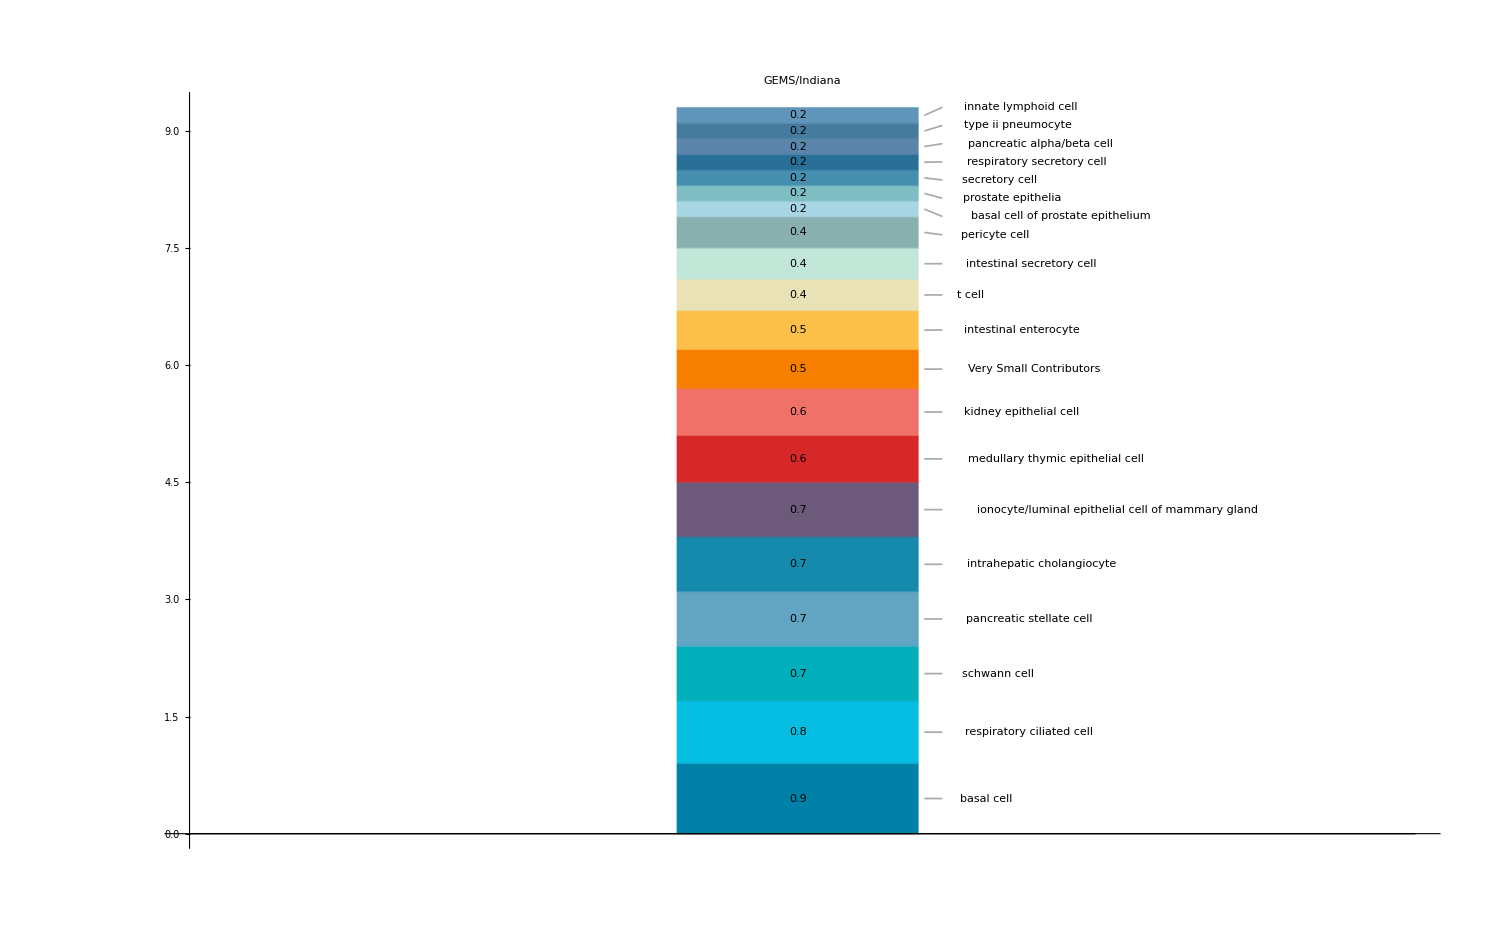

```mathematica
BarChart[shortlist,BarSpacing->2,ChartLayout->"Stacked",
ChartStyle-> barPal, ImageSize-> 1500, LabelingFunction ->( Placed[#1, Center]&), BaseStyle->{FontSize->15}, PlotLabel -> sampleCenter]
```

```mathematica
(* cool, now it's time to make the pie chart *)
```

```mathematica
gtPt1Percent = Position[Flatten[nonZeroVals], val_/;val  >=percentThresh ]
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12},{13},{14},{15},{16}}

```mathematica
bigContribs = Part[nonZeroVals, #] &/@ gtPt1Percent
```

{{27.5},{16.2},{10.4},{5.9},{5.7},{4.2},{3.7},{2.8},{2.4},{2.3},{2.2},{2.1},{1.6},{1.3},{1.2},{1.1}}

```mathematica
bigCells = Part[nonZeroCells, #] &/@ gtPt1Percent
```

{{erythrocyte/erythroid progenitor},{platelet},{monocyte},{nk cell},{b cell},{neutrophil},{endothelial cell},{mature conventional dendritic cell},{basophil},{adventitial cell},{thymocyte},{intestinal tuft cell},{cell of skeletal muscle},{salivary gland cell},{myeloid progenitor},{salivary/bronchial secretory cell}}

```mathematica
bigTot = Total[Flatten[bigContribs]] ;
smallContribTot = Total[Flatten[goodSmallVals]];
bigTot + smallContribTot (* cool, so we sum to 1 between small and big contributions *)
```

99.9

```mathematica
(* add the sum of the small contributions *)
```

```mathematica
bigContribs= AppendTo[bigContribs, {smallContribTot}];
bigCells = AppendTo[bigCells, {"Small"}]
```

{{erythrocyte/erythroid progenitor},{platelet},{monocyte},{nk cell},{b cell},{neutrophil},{endothelial cell},{mature conventional dendritic cell},{basophil},{adventitial cell},{thymocyte},{intestinal tuft cell},{cell of skeletal muscle},{salivary gland cell},{myeloid progenitor},{salivary/bronchial secretory cell},{Small}}

```mathematica
Total[Flatten[bigContribs]]
```

99.9

```mathematica
(* now it's time to sort it from big to small *)
```

```mathematica
finalOrderBig = Reverse[Ordering[bigContribs]];
bigContribs = Flatten[Part[bigContribs, #] &/@ finalOrderBig];
bigCells = Flatten[Part[bigCells, #] &/@ finalOrderBig];
```

```mathematica
(* make the labels for the pie chart *)
```

```mathematica
bigContribs
```

{27.5,16.2,10.4,9.3,5.9,5.7,4.2,3.7,2.8,2.4,2.3,2.2,2.1,1.6,1.3,1.2,1.1}

```mathematica
test = Callout[bigContribs[[#]], bigCells[[#]],  Appearance -> "Leader"]&/@ Range[Length[bigCells]]
```

{Callout[27.5,erythrocyte/erythroid progenitor,Appearance→Leader],Callout[16.2,platelet,Appearance→Leader],Callout[10.4,monocyte,Appearance→Leader],Callout[9.3,Small,Appearance→Leader],Callout[5.9,nk cell,Appearance→Leader],Callout[5.7,b cell,Appearance→Leader],Callout[4.2,neutrophil,Appearance→Leader],Callout[3.7,endothelial cell,Appearance→Leader],Callout[2.8,mature conventional dendritic cell,Appearance→Leader],Callout[2.4,basophil,Appearance→Leader],Callout[2.3,adventitial cell,Appearance→Leader],Callout[2.2,thymocyte,Appearance→Leader],Callout[2.1,intestinal tuft cell,Appearance→Leader],Callout[1.6,cell of skeletal muscle,Appearance→Leader],Callout[1.3,salivary gland cell,Appearance→Leader],Callout[1.2,myeloid progenitor,Appearance→Leader],Callout[1.1,salivary/bronchial secretory cell,Appearance→Leader]}

```mathematica
"#84a98c"
```

#84a98c

```mathematica
piePal = Map [RGBColor,{"#bee9e8" ,"#62b6cb","#1b4965","#cae9ff","#5fa8d3",  "#a4508b", "#BC412B","#f26419","#f8c7cc", "#f7567c","#7e1946", "#f6ae2d", "#68b0ab","#84a98c", "#5bba6f", "#9ece9a", "#c8d5b9", "#355070","#6d597a","#b56576","#e56b6f","#eaac8b","#89b0ae",  "#457b9d","#555b6e","#6096ba","#014f86"}]
```

{RGBColor[0.7450980392156863, 0.9137254901960784, 0.9098039215686274],RGBColor[0.3843137254901961, 0.7137254901960784, 0.796078431372549],RGBColor[0.10588235294117647, 0.28627450980392155, 0.396078431372549],RGBColor[0.792156862745098, 0.9137254901960784, 1.],RGBColor[0.37254901960784315, 0.6588235294117647, 0.8274509803921568],RGBColor[0.6431372549019608, 0.3137254901960784, 0.5450980392156862],RGBColor[0.7372549019607844, 0.2549019607843137, 0.16862745098039217],RGBColor[0.9490196078431372, 0.39215686274509803, 0.09803921568627451],RGBColor[0.9725490196078431, 0.7803921568627451, 0.8],RGBColor[0.9686274509803922, 0.33725490196078434, 0.48627450980392156],RGBColor[0.49411764705882355, 0.09803921568627451, 0.27450980392156865],RGBColor[0.9647058823529412, 0.6823529411764706, 0.17647058823529413],RGBColor[0.40784313725490196, 0.6901960784313725, 0.6705882352941176],RGBColor[0.5176470588235295, 0.6627450980392157, 0.5490196078431373],RGBColor[0.3568627450980392, 0.7294117647058823, 0.43529411764705883],RGBColor[0.6196078431372549, 0.807843137254902, 0.6039215686274509],RGBColor[0.7843137254901961, 0.8352941176470589, 0.7254901960784313],RGBColor[0.20784313725490197, 0.3137254901960784, 0.4392156862745098],RGBColor[0.42745098039215684, 0.34901960784313724, 0.47843137254901963],RGBColor[0.7098039215686275, 0.396078431372549, 0.4627450980392157],RGBColor[0.8980392156862745, 0.4196078431372549, 0.43529411764705883],RGBColor[0.9176470588235294, 0.6745098039215687, 0.5450980392156862],RGBColor[0.5372549019607843, 0.6901960784313725, 0.6823529411764706],RGBColor[0.27058823529411763, 0.4823529411764706, 0.615686274509804],RGBColor[0.3333333333333333, 0.3568627450980392, 0.43137254901960786],RGBColor[0.3764705882352941, 0.5882352941176471, 0.7294117647058823],RGBColor[0.00392156862745098, 0.30980392156862746, 0.5254901960784314]}

```mathematica
PieChart[test, ChartStyle->piePal, SectorOrigin->{ 8.3Pi / 10,1},BaseStyle->{FontSize->15},  ImageSize-> 1500,ImagePadding->{{240,60},{0,0}},LabelingFunction ->"RadialCenter", PlotLabel->sampleCenter]
```

-Graphics-

```mathematica
(* could try adding percents to the fractions but i wont *)
```

```mathematica
stringPercents = TextString[bigContribs[[#]]]<>"%" &/@ Range[Length[bigContribs]]
```

{27.5%,16.2%,10.4%,9.3%,5.9%,5.7%,4.2%,3.7%,2.8%,2.4%,2.3%,2.2%,2.1%,1.6%,1.3%,1.2%,1.1%}